```mathematica
cities={Entity["City",{"Miami","Florida","UnitedStates"}],Entity["City",{"SanDiego","California","UnitedStates"}],Entity["City",{"NewYork","NewYork","UnitedStates"}],
Entity["City",{"Chicago","Illinois","UnitedStates"}],Entity["City",{"Seattle","Washington","UnitedStates"}],Entity["City",{"SaltLakeCity","Utah","UnitedStates"}],Entity["City",{"Boston","Massachusetts","UnitedStates"}],Entity["City",{"Honolulu","Hawaii","UnitedStates"}],
Entity["City",{"Denver","Colorado","UnitedStates"}],Entity["City",{"Boulder","Colorado","UnitedStates"}]};
```

```mathematica
travelprices={343,612,221,279,784,709,221,1129,529,529};
```

```mathematica
distances=GeoDistance[Here,#]&/@cities
```

{875.037 mi,1959.63 mi,460.402 mi,349.941 mi,2086.87 mi,1564.7 mi,650.509 mi,4548.95 mi,1191.59 mi,1221.8 mi}

```mathematica
travelassociation=AssociationThread[cities->Transpose[{distances,travelprices}]]
```

<|Miami→{875.037 mi,343},San Diego→{1959.63 mi,612},New York City→{460.402 mi,221},Chicago→{349.941 mi,279},Seattle→{2086.87 mi,784},Salt Lake City→{1564.7 mi,709},Boston→{650.509 mi,221},Honolulu→{4548.95 mi,1129},Denver→{1191.59 mi,529},Boulder→{1221.8 mi,529}|>

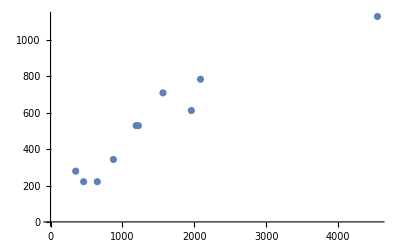

```mathematica
ListPlot[Tooltip[travelassociation[#],#]&/@cities]
```

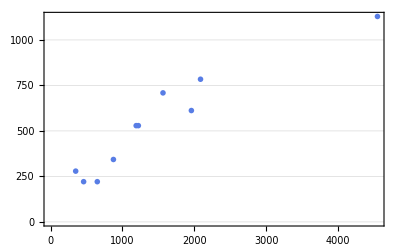

```mathematica
ListPlot[(Tooltip[travelassociation[#1],#1]&)/@cities,PlotTheme->"Business"]
```

```mathematica
Show[%56,Axes->True]
```

-Graphics-

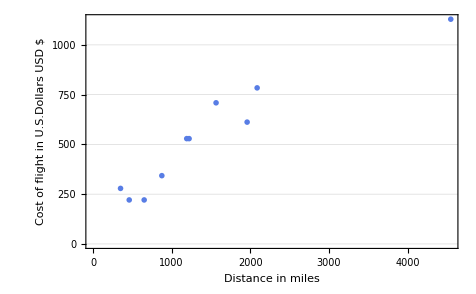

```mathematica
Show[%55,AxesLabel->{HoldForm[Distance in miles],HoldForm[Cost of flight in U.S.Dollars USD $]},LabelStyle->{FontFamily->"Arial",GrayLevel[0]}]
```

```mathematica
ListPlot[Tooltip[travelassociation[#],#]&/@cities]
```

-Graphics-

```mathematica
ListPlot[(Tooltip[travelassociation[#1],#1]&)/@cities,PlotTheme->"Business"]
```

-Graphics-

```mathematica
Show[%62,Axes->True]
```

-Graphics-

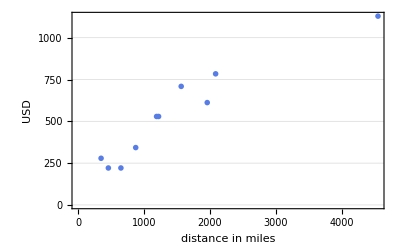

```mathematica
Show[%63,AxesLabel->{HoldForm[distance in miles],HoldForm[USD]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
ListPlot[Tooltip[travelassociation[#],#]&/@cities]
```

-Graphics-

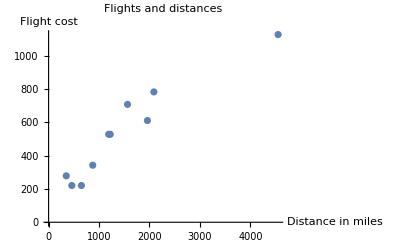

```mathematica
Show[%65,AxesLabel->{HoldForm[Distance in miles],HoldForm[Flight cost]},PlotLabel->HoldForm[Flights and distances],LabelStyle->{GrayLevel[0]}]
```